```mathematica
(*Top down*)
tmax=π/2.;
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/3d-grow-nedmovie/output/1/pack-line.txt",String];
NT2 =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/3d-grow-nedmovie/output/1/pack-force.txt",String];
tl={};
pl={};
tlist={};
hlist={};
xlist={};
mlist={};
xli={};
i=0;
i2=0;
sl={};
While[i<Length[NT],
i=i+1;
i2=i2+1;
current=StringSplit[NT[[i]]];
ti=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
ni=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
plist={};
ch={};
xh={};
sn=0;
For[j=0,j<ni,
i=i+1;
current=StringSplit[NT[[i]]];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
zj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
nxj=ToExpression[StringReplace[current[[4]],{"e+":>"*^","e-":>"*^-"}]];
nyj=ToExpression[StringReplace[current[[5]],{"e+":>"*^","e-":>"*^-"}]];
nzj=ToExpression[StringReplace[current[[6]],{"e+":>"*^","e-":>"*^-"}]];
nnorm=Sqrt[nxj*nxj+nyj*nyj+nzj*nzj];
nxj=nxj/nnorm;
nyj=nyj/nnorm;
nzj=nzj/nnorm;
lj=ToExpression[StringReplace[current[[7]],{"e+":>"*^","e-":>"*^-"}]];
sa=ToExpression[StringReplace[current[[9]],{"e+":>"*^","e-":>"*^-"}]];
AppendTo[ch,ArcSin[nzj]];
AppendTo[xh,xj];
c=RandomColor[];
c =RGBColor[{0,255,0}];
cs=Abs[ArcSin[nzj]]*255.0/(1.0*tmax);
If[cs>255,cs=255];
If[cs<0,cs=0];
c=RGBColor[{cs,0,255-cs}];
If[Abs[nzj]>0.5,c =RGBColor[{255,0,0}],c =RGBColor[{0,0,255}]];
c =RGBColor[{0,255,0}];
If[sa==1,
sn=sn+1;
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],c,Cylinder[{{xj-nxj*lj/2,yj-nyj*lj/2,zj-nzj*lj/2},{xj+nxj*lj/2,yj+nyj*lj/2,zj+nzj*lj/2}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],c,Sphere[{xj-nxj*lj/2,yj-nyj*lj/2,zj-nzj*lj/2},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],c,Sphere[{xj+nxj*lj/2,yj+nyj*lj/2,zj+nzj*lj/2},1]}]];
];
j=j+1;
];
AppendTo[sl,sn];
For[j=0,j<ni*(ni-1)/2,
i2=i2+1;
current=StringSplit[NT2[[i2]]];
x1=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
y1=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
x2=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
y2=ToExpression[StringReplace[current[[4]],{"e+":>"*^","e-":>"*^-"}]];
fmag=ToExpression[StringReplace[current[[5]],{"e+":>"*^","e-":>"*^-"}]];
cci=ToExpression[StringReplace[current[[6]],{"e+":>"*^","e-":>"*^-"}]];
ccj=ToExpression[StringReplace[current[[7]],{"e+":>"*^","e-":>"*^-"}]];
If[fmag>0&&cci==1&&ccj==1,
cx=Abs[fmag/1.5]*255;
If[cx>255,cx=255];
If[cx<0,cx=0];
cx=100;
c=RGBColor[{255-cx,cx,0}];
(*AppendTo[plist,Graphics3D[{Antialiasing->True,Black,c,Thickness[fmag*0.005],Line[{{x1,y1,15},{x2,y2,15}}]}]];*)
];
j=j+1;
];
AppendTo[xli,xh];
AppendTo[hlist,ch];
AppendTo[mlist,Mean[Re[Log10[ch]]]];
AppendTo[tlist,ti];
If[ti==0.00001,xlist=xh;
thl=ch;];
ml=25;
AppendTo[plist,Graphics3D[{Opacity[1],EdgeForm[],Brown,Cuboid[{{-ml,-ml,-5},{ml,ml,0}}]}]];
pi=Show[{plist},ImageSize->{600.,599.9950882942637},PlotRange->{{-ml,ml},{-ml,ml},{-5,ml}},ViewAngle->0.08434812670382222,ViewCenter->{{0.,0.,-5.},{-0.03445323858826432,-0.02774460237780696}},ViewPoint->{0.,0.,7.784301110271387},ViewVertical->{0.,1.,0.}];
AppendTo[tl,ti];
AppendTo[pl,pi];
];
ListAnimate[pl]
```

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/3-19-2017/low-friction-top.gif",pl,"DisplayDurations"->10./Length[pl]]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/3-19-2017/low-friction-top.gif

```mathematica
pl
```

{}

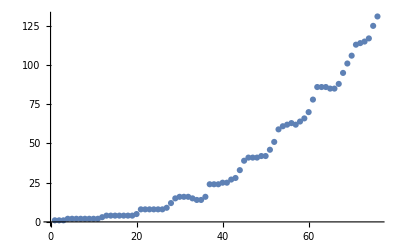

```mathematica
ListPlot[sl]
```

```mathematica
ListAnimate[pl]
```

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/3-19-2017/low-friction-side.gif",pl,"DisplayDurations"->0.5]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/wt_vis/force-net-sim2.gif

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/wt_vis/force-net-sim3.mov",ListAnimate[pl[[20;;30]],1],ImageResolution->800,Antialiasing->True,"VideoEncoding"->"Apple Intermediate Codec"]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/wt_vis/force-net-sim3.mov

```mathematica
Length[pl]
```

64

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/wt_vis/force-net-sim.gif",pl,"DisplayDurations"->{58/58.}]
```

ItemAspectRatio::shdw: Symbol ItemAspectRatio appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

/Users/farzanberoz/Desktop/biophysics/biofilms/wt_vis/force-net-sim.gif

```mathematica
pl[[-1]]
```

```mathematica
-Graphics3D-//Options
```

{ImageSize→{600.,599.995},PlotRange→{{-25,25},{-25,25},{-5,25}},ViewAngle→0.0843481,ViewCenter→{{0.,0.,-5.},{-0.0344532,-0.0277446}},ViewPoint→{0.,0.,7.7843},ViewVertical→{0.,1.,0.}}

```mathematica
(*Side*)
tmax=π/4.0;
L=12;
Nc=16;
s = 0.1;
Lx=2*Sqrt[Nc]*s;
Ly=(s*Sqrt[3.0]+3)*Sqrt[Nc];
NT =ReadList["/Users/farzanberoz/Desktop/biophysics/biofilms/3d-grow/output/biofilm-line.txt",String];
tl={};
pl={};
tlist={};
hlist={};
xlist={};
mlist={};
xli={};
i=0;
Length[NT]
While[i<Length[NT],
i=i+1;
current=StringSplit[NT[[i]]];
ti=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
ni=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
plist={};
ch={};
xh={};
For[j=0,j<ni,
i=i+1;
current=StringSplit[NT[[i]]];
xj=ToExpression[StringReplace[current[[1]],{"e+":>"*^","e-":>"*^-"}]];
yj=ToExpression[StringReplace[current[[2]],{"e+":>"*^","e-":>"*^-"}]];
zj=ToExpression[StringReplace[current[[3]],{"e+":>"*^","e-":>"*^-"}]];
nxj=ToExpression[StringReplace[current[[4]],{"e+":>"*^","e-":>"*^-"}]];
nyj=ToExpression[StringReplace[current[[5]],{"e+":>"*^","e-":>"*^-"}]];
nzj=ToExpression[StringReplace[current[[6]],{"e+":>"*^","e-":>"*^-"}]];
lj=ToExpression[StringReplace[current[[7]],{"e+":>"*^","e-":>"*^-"}]];
AppendTo[ch,ArcSin[nzj]];
AppendTo[xh,xj];
c=RandomColor[];
c =RGBColor[{0,255,0}];
cs=Abs[ArcSin[nzj]]*255.0/(1.0*tmax);
If[cs>255,cs=255];
If[cs<0,cs=0];
c=RGBColor[{cs,0,255-cs}];
For[qi=0,qi<1,
For[qj=0,qj<1,
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],c,Cylinder[{{xj-nxj*lj/2+Lx*qi+qj*Sqrt[Nc]*s,yj-nyj*lj/2+Ly*qj,zj-nzj*lj/2},{xj+nxj*lj/2+Lx*qi+qj*Sqrt[Nc]*s,yj+nyj*lj/2+Ly*qj,zj+nzj*lj/2}},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],c,Sphere[{xj-nxj*lj/2+Lx*qi+qj*Sqrt[Nc]*s,yj-nyj*lj/2+Ly*qj,zj-nzj*lj/2},1]}]];
AppendTo[plist,Graphics3D[{Specularity[White,15],Opacity[1],EdgeForm[],c,Sphere[{xj+nxj*lj/2+Lx*qi+qj*Sqrt[Nc]*s,yj+nyj*lj/2+Ly*qj,zj+nzj*lj/2},1]}]];
qj=qj+1;
];
qi=qi+1;
];
j=j+1;
];
AppendTo[xli,xh];
AppendTo[hlist,ch];
AppendTo[mlist,Mean[Re[Log10[ch]]]];
AppendTo[tlist,ti];
If[ti==0.00001,xlist=xh;
thl=ch;];
ml=25;
AppendTo[plist,Graphics3D[{Opacity[1],EdgeForm[],Brown,Cuboid[{{-ml,-ml,-5},{ml,ml,0}}]}]];
pi=Show[{plist},ImageSize->600,ViewCenter->{0,0,-5 },ViewPoint->{-1.430802273820603,-18.80105053806243,6.743389616391173},
PlotRange->{{-ml,ml},{-ml,ml},{-5,ml}}];
AppendTo[tl,ti];
AppendTo[pl,pi];
];
ListAnimate[pl]
```

1063

```mathematica
Length[pl]
```

47

```mathematica
tlist
```

{}

```mathematica
k
```

```mathematica
Length[Take[pl,{1,-1,4}]]
```

459

```mathematica
Length[Take[pl,{1,150}]]
```

```mathematica
Length[pl]
```

809

```mathematica
ListAnimate[pl]
```

$Aborted[]

```mathematica
hlist[[1]]
xli[[1]]
```

{1.8138×10^-7,2.63808×10^-7,9.77057×10^-8,2.84285×10^-7,-2.17844×10^-7,-7.17776×10^-8,-2.74871×10^-7,-1.28454×10^-7,-2.88209×10^-7,-3.4103×10^-7,-9.93857×10^-8,-1.90756×10^-7,3.8224×10^-7,1.43751×10^-7,-1.86867×10^-7,4.04247×10^-7,-3.69267×10^-7,2.51739×10^-7,1.08147×10^-7,2.99256×10^-7,-1.9821×10^-7,2.5929×10^-7,-3.74742×10^-7,3.55853×10^-7,-5.47411×10^-8,-2.9901×10^-7,3.44255×10^-7,4.76861×10^-7,3.45519×10^-7,4.11727×10^-7,3.74828×10^-7,3.99665×10^-7,-3.57513×10^-7,3.43395×10^-7,3.89856×10^-7,-2.99531×10^-7,1.76683×10^-7,-4.10482×10^-7,-9.50377×10^-8,2.36881×10^-7,3.84545×10^-7,-3.46021×10^-7,1.63652×10^-7,9.40381×10^-8,-4.04804×10^-7,-1.33013×10^-7,-1.32764×10^-7,2.86789×10^-7,-3.91327×10^-7,-3.01988×10^-8,4.17957×10^-7,3.63648×10^-7,2.61269×10^-7,9.07004×10^-8,2.70536×10^-7,1.70439×10^-7,3.74964×10^-8,-7.06691×10^-8,-1.08937×10^-7,2.25167×10^-7,1.45825×10^-7,2.46937×10^-7,-1.05714×10^-7,-1.65889×10^-7}

{}

```mathematica
Length[xli]
```

19

```mathematica
|
```

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/3d-film/analysis/plots/larger-scale-1d-expansion.gif",Take[pl,{1,-1,4}],"DisplayDurations"->{10/224.}]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/3d-film/analysis/plots/larger-scale-1d-expansion.gif

```mathematica
Length[Take[pl,{1,60}]]
```

60

```mathematica
Length[pl]
```

271

```mathematica
Length[Take[pl,{1,-1,2}]]
```

136

```mathematica
Export["/Users/farzanberoz/Desktop/biophysics/biofilms/3d-dynamical/analysis/plots/2d-packing-15.gif",Take[pl,{1,-1,2}],"DisplayDurations"->{10./136.}]
```

/Users/farzanberoz/Desktop/biophysics/biofilms/3d-dynamical/analysis/plots/2d-packing-15.gif

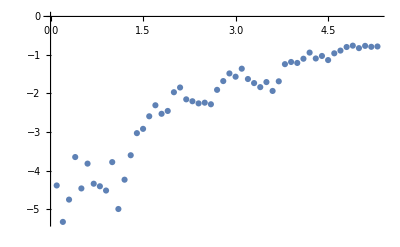

```mathematica
ListPlot[Transpose[{tlist,mlist}],PlotRange->{Automatic,Automatic},LabelStyle->Large]
```

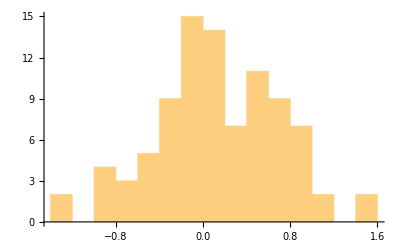

```mathematica
Histogram[hlist[[-1]],15]
```